# Lab 6: Modules, Interpolation and Texture Mapping

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True]
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot,ListPlot},ImageSize->Small,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Problem 1 *)
```

```mathematica
f1[a_,b_]:=Module[{s},s=a+b;s]
```

```mathematica
f1[5,2]
```

7

```mathematica
(* Problem 2 *)
```

```mathematica
f2[h1_,h2_,A_]:=Module[{x},x=h1[A]+h2[A]+A^2;x]
```

```mathematica
h1[x_]:=x^2
h2[x_]:=Sin[x]
```

```mathematica
f2[h1,h2,A]
```

2 A^2+Sin[A]

```mathematica
f2[h1,h2,Pi]
```

2 π^2

```mathematica
(* Problem 3 *)
```

```mathematica
f3[n_]:=Module[{s},s=Sum[i,{i,n}];s]
```

```mathematica
f3[5]
```

15

```mathematica
(* Problem 4 *)
```

```mathematica
data4={1,4,5,6,8,9,1,9,7}
```

{1,4,5,6,8,9,1,9,7}

```mathematica
f4[data_]:=Module[{f},f:=Interpolation[data,Method->"Spline"];f]
```

```mathematica
myf=f4[data4]
```

InterpolatingFunction[…]

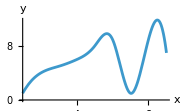

```mathematica
Plot[myf[t],{t,1,Length[data4]}]
```

```mathematica
(* Problem 5 *)
```

```mathematica
data5={{1,2},{4,4},{6,5},{0,0},{2,2}}
```

{{1,2},{4,4},{6,5},{0,0},{2,2}}

```mathematica
f5[data_]:=Module[{f,px,py,x,y},
px=Transpose[data][[1]];
py=Transpose[data][[2]];
x=Interpolation[px,Method->"Spline"];
y=Interpolation[py,Method->"Spline"];
f={x[#1],y[#1]}&;
f]
```

```mathematica
Off[InterpolatingFunction::dmval]
```

```mathematica
Myf5=f5[data5]
```

{x$9079[#1],y$9079[#1]}&

```mathematica
dd=Dimensions[data5][[1]]
```

5

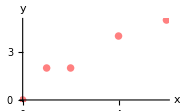

```mathematica
pp=ListPlot[data5,PlotStyle->{Pink,PointSize[0.03]}]
```

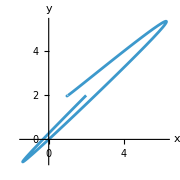

```mathematica
p5=ParametricPlot[f5[data5][t],{t,1,dd}]
```

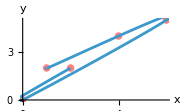

```mathematica
Show[pp,p5]
```

```mathematica
(* Problem 6 *)
```

```mathematica
GL2[s1_,s2_]:=Module[{L,L1,G1,G2,GAll,t},L[t_]:=s1*(1-t)+s2*t;
L1=ParametricPlot[L[t],{t,-5,5}];
G1:=Graphics[{Red,Point[s1]}];
G2:=Graphics[{Red,Point[s2]}];
GAll=Show[{L1,G1,G2}];
GAll]
```

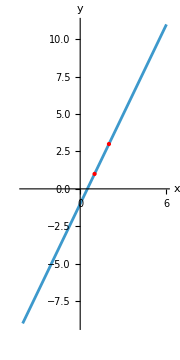

```mathematica
GL2[{1,1},{2,3}]
```

```mathematica
(* Problem 0 *)
```

```mathematica
Text0:=-Graphics-
```

```mathematica
a=2.5;
```

```mathematica
s0[u_,v_]:={(3+Cos[a*v])*Sin[u],(3+Cos[v])*Cos[u],Sin[v]}
```

```mathematica
G0=ParametricPlot3D[s0[u,v],{u,0,2*Pi},{v,0,2*Pi},PlotStyle->Texture[Text0],Mesh->False]
```

-Graphics3D-

```mathematica
Zero=Graphics3D[{Red,PointSize[0.08],Point[{{0,0,0}}]}]
```

-Graphics3D-

```mathematica
Show[G0,Zero]
```

-Graphics3D-

```mathematica
data0:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
xd0=Transpose[data0][[1]];
yd0=Transpose[data0][[2]];
zd0=Transpose[data0][[3]];
sd0x=Interpolation[xd0,Method->"Spline"];
sd0y=Interpolation[yd0,Method->"Spline"];
sd0z=Interpolation[zd0,Method->"Spline"];
```

```mathematica
Traj0[t_]={sd0x[t],sd0y[t],sd0z[t]}
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
L0=Length[xd0];
```

```mathematica
plot0t=ParametricPlot3D[Traj0[t],{t,1,L0},PlotStyle->Purple ];
```

```mathematica
plot0tpoints=ListPointPlot3D[data0,PlotStyle->{PointSize[0.01],Blue}];
```

```mathematica
GTraj0=Show[{plot0t,plot0tpoints}]
```

-Graphics3D-

```mathematica
plots0[s_]:=ParametricPlot3D[s0[u,v]+Traj0[s],{u,0,2*Pi},{v,0,2*Pi},PlotStyle->Texture[Text0],Mesh->False]
```

```mathematica
Manipulate[Show[{GTraj0,plots0[s]},PlotRange->10],{s,1,L0}]
```

```mathematica
Text01:=-Graphics-;Text11:=-Graphics-;Text12:=-Graphics-
```

```mathematica
Tex={Text01,Text11,Text12}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotsT[s_,Tex_]:=ParametricPlot3D[s0[u,v]+Traj0[s],{u,0,2*Pi},{v,0,2*Pi},PlotStyle->Texture[Tex],Mesh->False]
```

```mathematica
Manipulate[Show[{GTraj0,plotsT[s,t]},PlotRange->10],{s,1,L0},{t,Tex}]
```

```mathematica
(* Problem (1) Interpolate a 3D data given by the heights of the explicit function z=f(x,y) using the synthetic data
data1=Table[Round[Exp[x2-y^2],0.01]{x,-1,1,0.25},{y,-1,2,0.25}]
Move the resulting surface along an interpolated curve 
through points pp1={0,0,0} and pp2={1,1,1} pp3={0.5,0.5,0.5}; pp4={0,3,2} 
 ListInterpolation[data,{{xmin,xmax,{ymin,ymax}}]
*)
```

```mathematica
pp1={0,0,0} ; pp2={1,0,0.5};pp3={0.7,0.8,0.9};pp4={0,3,2};
```

```mathematica
fsyn[x_,y_]:=x y Exp[x^2- y^2]
```

```mathematica
xmin1=-1;xmax1=1;ymin1=-1;ymax1=1;
```

```mathematica
stepx1=0.25;stepy1=stepx1;
```

```mathematica
data1=Table[Round[fsyn[x,y],0.01],{x,xmin1,xmax1,stepx1},{y,ymin1,ymax1,stepy1}];
```

```mathematica
MatrixForm[data1]
```

(1. | 1.16 | 1.06 | 0.64 | 0. | -0.64 | -1.06 | -1.16 | -1.
0.48 | 0.56 | 0.51 | 0.31 | 0. | -0.31 | -0.51 | -0.56 | -0.48
0.24 | 0.27 | 0.25 | 0.15 | 0. | -0.15 | -0.25 | -0.27 | -0.24
0.1 | 0.11 | 0.1 | 0.06 | 0. | -0.06 | -0.1 | -0.11 | -0.1
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.1 | -0.11 | -0.1 | -0.06 | 0. | 0.06 | 0.1 | 0.11 | 0.1
-0.24 | -0.27 | -0.25 | -0.15 | 0. | 0.15 | 0.25 | 0.27 | 0.24
-0.48 | -0.56 | -0.51 | -0.31 | 0. | 0.31 | 0.51 | 0.56 | 0.48
-1. | -1.16 | -1.06 | -0.64 | 0. | 0.64 | 1.06 | 1.16 | 1.)

```mathematica
data1
```

{{1.,1.16,1.06,0.64,0.,-0.64,-1.06,-1.16,-1.},{0.48,0.56,0.51,0.31,0.,-0.31,-0.51,-0.56,-0.48},{0.24,0.27,0.25,0.15,0.,-0.15,-0.25,-0.27,-0.24},{0.1,0.11,0.1,0.06,0.,-0.06,-0.1,-0.11,-0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.1,-0.11,-0.1,-0.06,0.,0.06,0.1,0.11,0.1},{-0.24,-0.27,-0.25,-0.15,0.,0.15,0.25,0.27,0.24},{-0.48,-0.56,-0.51,-0.31,0.,0.31,0.51,0.56,0.48},{-1.,-1.16,-1.06,-0.64,0.,0.64,1.06,1.16,1.}}

```mathematica
DR1
```

DR1

```mathematica
(* x-y-range *)
```

```mathematica
DR1={{xmin1,xmax1},{ymin1,ymax1}};
```

```mathematica
GD1=ListPointPlot3D[data1,PlotStyle->{Orange,PointSize[0.05]},DataRange->DR1]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{{1.,1.16,1.06,0.64,0.,-0.64,-1.06,-1.16,-1.},{1.,1.16,1.06,0.64,0.,-0.64,-1.06,-1.16,-1.}}]
```

-Graphics3D-

```mathematica
(* Transpose the matrix to comply with ListInterpolation. *)
```

```mathematica
Tdata1=Transpose[data1];
```

```mathematica
f1=ListInterpolation[Tdata1,DR1]
```

InterpolatingFunction[…]

```mathematica
Zero=Graphics3D[{Red,PointSize[0.08],Point[{{0,0,0}}]}];
```

```mathematica
(* Plot the surface *)
```

```mathematica
TextEl=-Graphics-;
```

```mathematica
Ginter=Plot3D[f1[x,y],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotStyle->{Blue,Opacity[0.7],Texture[TextEl]}]
```

-Graphics3D-

```mathematica
(* Superimpose  *)
```

```mathematica
GAll=Show[{GD1,Ginter,Zero},Boxed->True]
```

-Graphics3D-

```mathematica
(* Understand the structure of the modules below  *)
```

```mathematica
Listp=2{pp1,pp2,pp3,pp4}
```

{{0,0,0},{2,0,1.},{1.4,1.6,1.8},{0,6,4}}

```mathematica
(* Extract x,y,z from the data  *)
```

```mathematica
Extractxyz[data_]:=Module[{dataT,px,py,pz},
dataT=Transpose[data];
px=dataT[[1]];
py=dataT[[2]];
pz=dataT[[3]];
{px,py,pz}(*output=x,y,z*)]
```

```mathematica
{px,py,pz}=Extractxyz[Listp]
```

{{0,2,1.4,0},{0,0,1.6,6},{0,1.,1.8,4}}

```mathematica
(* Generate fx,fy,fz to compose a parametric function Traj1[s]  fill 4 lines here*)
```

```mathematica
Interpxyz[data_]:=Module[{px,py,pz,fx,fy,fz},
{px,py,pz}=Extractxyz[data]; 
fx=Interpolation[px,Method->"Spline"];
fy=Interpolation[py,Method->"Spline"];
fz=Interpolation[pz,Method->"Spline"];{fx,fy,fz}]
```

```mathematica
{tx,ty,tz}=Interpxyz[Listp]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Traj1[s_]:={tx[s],ty[s],tz[s]}
```

```mathematica
GL1=ParametricPlot3D[Traj1[t],{t,1,4}]
```

-Graphics3D-

```mathematica
(* The line and the surface  *)
```

```mathematica
SG11=Show[GL1,Ginter]
```

-Graphics3D-

```mathematica
(* Convert the surface into the parametric form  *)
```

```mathematica
S1[u_,v_]:={u,v,f1[u,v]}
```

```mathematica
(* Check  *)
```

```mathematica
GP1=ParametricPlot3D[S1[x,y],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotRange->1,BoxRatios->1]
```

-Graphics3D-

```mathematica
SurfacePosition1[u_,v_,t_]:=S1[u,v]+Traj1[t]
```

```mathematica
(* Check  *)
```

```mathematica
SurfacePosition1[1,1,1]
```

{1.,1.,1.}

```mathematica
Text1:=-Graphics-
```

```mathematica
Gfunction1[t_]:=ParametricPlot3D[SurfacePosition1[x,y,t],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotStyle->Texture[Text1],Mesh->False]
```

```mathematica
(* Check  *)
```

```mathematica
Gfunction1[2.5]
```

-Graphics3D-

```mathematica
GShowAll[s_]:=Show[{GL1,Zero,Gfunction1[s]},PlotRange->{{-2,3},{-1,10},{0,5}}]
```

```mathematica
Manipulate[GShowAll[t],{t,1,4}]
```

```mathematica
(* Problem 2 *)
```

```mathematica
data0=Table[{Sin[3*t],Cos[2*t],t},{t,0,5,0.25}]
```

{{0.,1.,0.},{0.681639,0.877583,0.25},{0.997495,0.540302,0.5},{0.778073,0.0707372,0.75},{0.14112,-0.416147,1.},{-0.571561,-0.801144,1.25},{-0.97753,-0.989992,1.5},{-0.858934,-0.936457,1.75},{-0.279415,-0.653644,2.},{0.450044,-0.210796,2.25},{0.938,0.283662,2.5},{0.922604,0.70867,2.75},{0.412118,0.96017,3.},{-0.319519,0.976588,3.25},{-0.879696,0.753902,3.5},{-0.967808,0.346635,3.75},{-0.536573,-0.1455,4.},{0.182599,-0.602012,4.25},{0.803784,-0.91113,4.5},{0.993641,-0.997172,4.75},{0.650288,-0.839072,5.}}

```mathematica
ppp=ListPointPlot3D[data0]
```

-Graphics3D-

```mathematica
Extractxyz[data0]
```

{{0.,0.681639,0.997495,0.778073,0.14112,-0.571561,-0.97753,-0.858934,-0.279415,0.450044,0.938,0.922604,0.412118,-0.319519,-0.879696,-0.967808,-0.536573,0.182599,0.803784,0.993641,0.650288},{1.,0.877583,0.540302,0.0707372,-0.416147,-0.801144,-0.989992,-0.936457,-0.653644,-0.210796,0.283662,0.70867,0.96017,0.976588,0.753902,0.346635,-0.1455,-0.602012,-0.91113,-0.997172,-0.839072},{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}}

```mathematica
{tx1,ty1,tz1}=Interpxyz[data0]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Length[data0]
```

21

```mathematica
GL1=ParametricPlot3D[{tx1[t],ty1[t],tz1[t]},{t,1,Length[data0]}]
```

-Graphics3D-

```mathematica
pp5[t_]:=Graphics3D[{Blue,Octahedron[{tx1[t],ty1[t],tz1[t]},1]}]
```

```mathematica
Manipulate[Show[{GL1,pp5[t]},PlotRange->{{-2,2},{-2,2},{0,4}}],{t,1,Length[data0]}]
```

```mathematica
(* Bonus *)
```

```mathematica
S[x_,y_]:=Sin[x*y/20]
```

```mathematica
s1=Plot3D[S[x,y],{x,-10,10},{y,-10,10},PlotStyle->{Yellow,Opacity[0.5]}]
```

-Graphics3D-

```mathematica
DR1
```

{{-1,1},{-1,1}}

```mathematica
GD1=ListPointPlot3D[data1,PlotStyle->{Orange,PointSize[0.05]},DataRange->DR1]
```

-Graphics3D-

```mathematica
data1=Table[Round[fsyn[x,y],0.01],{x,xmin1,xmax1,stepx1},{y,ymin1,ymax1,stepy1}];
```

```mathematica
data1
```

{{1.,1.16,1.06,0.64,0.,-0.64,-1.06,-1.16,-1.},{0.48,0.56,0.51,0.31,0.,-0.31,-0.51,-0.56,-0.48},{0.24,0.27,0.25,0.15,0.,-0.15,-0.25,-0.27,-0.24},{0.1,0.11,0.1,0.06,0.,-0.06,-0.1,-0.11,-0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.1,-0.11,-0.1,-0.06,0.,0.06,0.1,0.11,0.1},{-0.24,-0.27,-0.25,-0.15,0.,0.15,0.25,0.27,0.24},{-0.48,-0.56,-0.51,-0.31,0.,0.31,0.51,0.56,0.48},{-1.,-1.16,-1.06,-0.64,0.,0.64,1.06,1.16,1.}}

```mathematica
data=Table[S[x,y],{x,-10,10,5},{y,-10,10,5}];
s2=ListPointPlot3D[data,PlotStyle->{Blue,PointSize[0.1]}]
```

-Graphics3D-

```mathematica
PlotSpheres[S_,N_,RS_]:=Module[{sur,step,points,pointsf,sphereAll,result,p},
sur=Plot3D[S[x,y],{x,-10,10},{y,-10,10},PlotStyle->{Yellow,Opacity[0.5]}];
step=20/(N-1);
p[i_]:=-10+step*(i-1);
points=Table[{p[i],p[j],S[p[i],p[j]]+RS},{i,N},{j,N}];
pointsf=Flatten[points,1];
sphereAll=Graphics3D[{Blue,Sphere[pointsf,RS]}];
result=Show[{sphereAll,sur},PlotRange->Automatic];
result]
```

```mathematica
S[x_,y_]:=Sin[x*y/20]
```

```mathematica
PlotSpheres[S,5,1.5]
```

-Graphics3D-

```mathematica
PlotSpheres1[S_,N_,RS_]:=Module[{s1,s2,data,res},
s1=Plot3D[S[x,y],{x,-10,10},{y,-10,10},PlotStyle->{Yellow,Opacity[0.5]}];
data=Table[S[x,y],{x,-10,10,20/(N-1)},{y,-10,10,20/(N-1)}];
s2=ListPointPlot3D[data,PlotStyle->{Blue,PointSize[RS]}];
res=Show[{s1,s2}];
res]
```

```mathematica
PlotSpheres1[S,5,0.1]
```

-Graphics3D-